```mathematica
filelist=("E:\\_time_varying_data\\SmokeSim\\tif\\dsSmoke."<>IntegerString[#,10,3]<>".tif")&/@Range[0,499];
d=Import[filelist[[#]],"Image3D"]&/@Range[1,500];
```

```mathematica
offset=9;
tf=ColorData["RedGreenSplit"]
tffilelist=("E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke."<>IntegerString[#,10,3]<>".tfi")&/@Range[0,499];
```

ColorDataFunction[…]

```mathematica
i=160
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
a=Flatten[ImageData[d[[i]]]];
b=Flatten[ImageData[std]];
h=HistogramList[a]
x=Take[h[[1]],Length[h[[1]]]-1]
y=h[[2]]
p=ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]
Export[NotebookDirectory[]<>"smoke2\\"<>ToString[160]<>".png",p,ImageSize->640];
```

160

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20},{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}}

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}

-Graphics-

```mathematica
bins=ConstantArray[0,Length[y]]
sumstd=ConstantArray[0,Length[y]]
Table[j=IntegerPart[a[[i]]*20]+1;bins[[j]]++;sumstd[[j]]+=b[[i]],{i,1,Length[a]}];
bins
sumstd
stds=sumstd/bins
p2=ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"]
Export[NotebookDirectory[]<>"smoke2\\"<>ToString[160]<>"_std.png",p2,ImageSize->640];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}

{554.11,386.004,266.243,222.243,188.902,167.631,143.827,109.843,107.451,97.298,93.8196,71.5451,64.0431,58.1647,45.3137,28.549,20.8863,9.60392,3.93333,0.721569,0.}

{0.000592688,0.0194735,0.0302549,0.0391135,0.0449874,0.0492309,0.0505012,0.0500424,0.0500937,0.0495913,0.049904,0.04667,0.0414519,0.0377938,0.0293673,0.02264,0.0151022,0.00830789,0.00392548,0.00106583,0.}

-Graphics-

160

{{0,-Graphics-},{0.0588235,-Graphics-},{0.117647,-Graphics-},{0.176471,-Graphics-},{0.235294,-Graphics-},{0.294118,-Graphics-},{0.352941,-Graphics-},{0.411765,-Graphics-},{0.470588,-Graphics-},{0.529412,-Graphics-},{0.588235,-Graphics-},{0.647059,-Graphics-},{0.705882,-Graphics-},{0.764706,-Graphics-},{0.823529,-Graphics-},{0.882353,-Graphics-},{0.941176,-Graphics-},{1,-Graphics-}}

Blend[intensitycolors,#1]&

{{0,-Graphics-},{0.0588235,-Graphics-},{0.117647,-Graphics-},{0.176471,-Graphics-},{0.235294,-Graphics-},{0.294118,-Graphics-},{0.352941,-Graphics-},{0.411765,-Graphics-},{0.470588,-Graphics-},{0.529412,-Graphics-},{0.588235,-Graphics-},{0.647059,-Graphics-},{0.705882,-Graphics-},{0.764706,-Graphics-},{0.823529,-Graphics-},{0.882353,-Graphics-},{0.941176,-Graphics-},{1,-Graphics-}}

Blend[intensitycolors2,#1]&

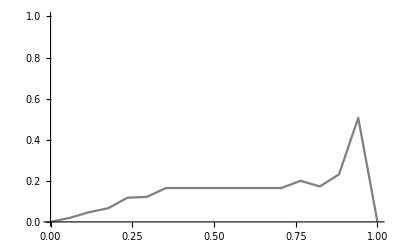

-Graphics3D-

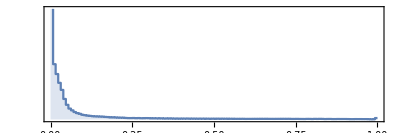

```mathematica
i
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
intensitycolors=Transpose[{intensity,colors}]
defaultcolorfunction=(Blend[{{0., RGBColor[0.05635, 0.081, 0.07687, 0.0166234]}, {0.1, RGBColor[0.8877, 0.2636, 0., 0.114961]}, {0.66, RGBColor[1., 0.9658, 0.4926, 0.665652]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & );
colorfunction=(Blend[intensitycolors, #1] & )
rgb=(#/255.&)/@Transpose[{r,g,b}];
colors2=RGBColor/@rgb;
intensitycolors2=Transpose[{intensity,colors2}]
colorfunction2=(Blend[intensitycolors2, #1] & )
opacity=(#/255.&)/@a;
ListLinePlot[Transpose[{intensity,opacity}],PlotRange->{{0,1},{0,1}},ColorFunction->colorfunction2,PlotLegends->"transfer function"]
Image3D[d[[i]],ColorFunction->colorfunction]
ImageHistogram[d[[i]]]
```

```mathematica
list=Range[0,1,1/255]
Length[list]
```

{0,1/255,2/255,1/85,4/255,1/51,2/85,7/255,8/255,3/85,2/51,11/255,4/85,13/255,14/255,1/17,16/255,1/15,6/85,19/255,4/51,7/85,22/255,23/255,8/85,5/51,26/255,9/85,28/255,29/255,2/17,31/255,32/255,11/85,2/15,7/51,12/85,37/255,38/255,13/85,8/51,41/255,14/85,43/255,44/255,3/17,46/255,47/255,16/85,49/255,10/51,1/5,52/255,53/255,18/85,11/51,56/255,19/85,58/255,59/255,4/17,61/255,62/255,21/85,64/255,13/51,22/85,67/255,4/15,23/85,14/51,71/255,24/85,73/255,74/255,5/17,76/255,77/255,26/85,79/255,16/51,27/85,82/255,83/255,28/85,1/3,86/255,29/85,88/255,89/255,6/17,91/255,92/255,31/85,94/255,19/51,32/85,97/255,98/255,33/85,20/51,101/255,2/5,103/255,104/255,7/17,106/255,107/255,36/85,109/255,22/51,37/85,112/255,113/255,38/85,23/51,116/255,39/85,118/255,7/15,8/17,121/255,122/255,41/85,124/255,25/51,42/85,127/255,128/255,43/85,26/51,131/255,44/85,133/255,134/255,9/17,8/15,137/255,46/85,139/255,28/51,47/85,142/255,143/255,48/85,29/51,146/255,49/85,148/255,149/255,10/17,151/255,152/255,3/5,154/255,31/51,52/85,157/255,158/255,53/85,32/51,161/255,54/85,163/255,164/255,11/17,166/255,167/255,56/85,169/255,2/3,57/85,172/255,173/255,58/85,35/51,176/255,59/85,178/255,179/255,12/17,181/255,182/255,61/85,184/255,37/51,62/85,11/15,188/255,63/85,38/51,191/255,64/85,193/255,194/255,13/17,196/255,197/255,66/85,199/255,40/51,67/85,202/255,203/255,4/5,41/51,206/255,69/85,208/255,209/255,14/17,211/255,212/255,71/85,214/255,43/51,72/85,217/255,218/255,73/85,44/51,13/15,74/85,223/255,224/255,15/17,226/255,227/255,76/85,229/255,46/51,77/85,232/255,233/255,78/85,47/51,236/255,79/85,14/15,239/255,16/17,241/255,242/255,81/85,244/255,49/51,82/85,247/255,248/255,83/85,50/51,251/255,84/85,253/255,254/255,1}

256

```mathematica
(*start=1+offset;end=500;step=20;
Do[
end2=Min[j+step-1,end];
Module[{list,std,a,b,h,x,y,bins,sumstd,stds},
Table[
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
a=Flatten[ImageData[d[[i]]]];
b=Flatten[ImageData[std]];
h=HistogramList[a];
x=Take[h[[1]],Length[h[[1]]]-1];
y=h[[2]];
ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]//
Export[NotebookDirectory[]<>"smoke2\\"<>ToString[i]<>".png",#,ImageSize->{640,280}]&;
bins=ConstantArray[0,Length[y]];
sumstd=ConstantArray[0,Length[y]];
Table[n=IntegerPart[a[[m]]*20]+1;bins[[n]]++;sumstd[[n]]+=b[[m]],{m,1,Length[a]}];
stds=sumstd/bins;
ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"]//
Export[NotebookDirectory[]<>"smoke2_std\\"<>ToString[i]<>".png",#,ImageSize->{640,280}]&
,{i,j,end2}]
]
,{j,start,end,step}]*)
```